```mathematica
ClearAll["Global`*"]
(*"complicated form" where we account for chance individuals select each other*)
E11 = (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2)) - (b^2*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))^2
E12 = n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) - n2 /(( b(n1-1)+n2 + (n-n1-n2)) *  (n1+b(n2-1)+(n-n1-n2)))^2
n1 = n2 = d / 2 * n
```

-(b^2 (-1+n1))/(n+b (-1+n1)-n1)^2+(2 b (-1+n1))/(n+b (-1+n1)-n1)

n2/(n+b (-1+n1)-n1)-n2/((n+b (-1+n1)-n1)^2 (n+b (-1+n2)-n2)^2)+n2/(n+b (-1+n2)-n2)

(d n)/2

```mathematica
(*"simple form" where we do NOT account for chance individuals select each other*)
E11 = (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))
E12 = n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2))
```

(2 b (-1+(d n)/2))/(n-(d n)/2+b (-1+(d n)/2))

(d n)/(n-(d n)/2+b (-1+(d n)/2))

```mathematica
(2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2)) - (b^2*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))^2==n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) - n2 /(( b(n1-1)+n2 + (n-n1-n2)) *  (n1+b(n2-1)+(n-n1-n2)))^2
```

-(b^2 (-1+(d n)/2))/(n-(d n)/2+b (-1+(d n)/2))^2+(2 b (-1+(d n)/2))/(n-(d n)/2+b (-1+(d n)/2))==-(d n)/(2 (n-(d n)/2+b (-1+(d n)/2))^4)+(d n)/(n-(d n)/2+b (-1+(d n)/2))

```mathematica
(*Let's assume complicated form where we account for chance individuals select each other*)
(*Solve[ (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2)) - (b^2*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))^2==n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) - n2 /(( b(n1-1)+n2 + (n-n1-n2)) *  (n1+b(n2-1)+(n-n1-n2)))^2 , b]*)
Solve[ (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2)) - (b^2*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))^2==n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) - n2 /(( b(n1-1)+n2 + (n-n1-n2)) *  (n1+b(n2-1)+(n-n1-n2))) , n]
```

{{n→(4 b-d-4 b d+5 b^2 d-√(16 b^2-8 b d+16 b^2 d-8 b^3 d+d^2+8 b d^2-18 b^2 d^2+8 b^3 d^2+b^4 d^2))/(2 (-2 d+2 b d+d^2-2 b d^2+b^2 d^2))},{n→(4 b-d-4 b d+5 b^2 d+√(16 b^2-8 b d+16 b^2 d-8 b^3 d+d^2+8 b d^2-18 b^2 d^2+8 b^3 d^2+b^4 d^2))/(2 (-2 d+2 b d+d^2-2 b d^2+b^2 d^2))}}

```mathematica
(2 n-2 d n-d n^2+d^2 n^2+√(-4+8 d n+4 n^2-4 d n^2-4 d n^3+d^2 n^4))/(2-4 d n+d^2 n^2)/.{n->80, d->0.8}
(2 b-2 b d+2 b^2 d+√2 √(2 b^2+2 d-2 b d-2 b^2 d+2 b^3 d-d^2+2 b d^2-2 b^3 d^2+b^4 d^2))/(-2 d+2 b d+d^2-2 b d^2+b^2 d^2)/.{b->1.1, d->0.8}
```

1.03227

27.5951

```mathematica
Simplify[(2 b-2 b d+2 b^2 d+√2 √(2 b^2+2 d-2 b d-2 b^2 d+2 b^3 d-d^2+2 b d^2-2 b^3 d^2+b^4 d^2))/(-2 d+2 b d+d^2-2 b d^2+b^2 d^2),{b>1, d>0}]
```

(-2 b (-1+d)+2 b^2 d+√(-4 b^2 (-1+d)-2 (-2+d) d+4 b (-1+d) d-4 b^3 (-1+d) d+2 b^4 d^2))/((-1+b) d (2+(-1+b) d))

```mathematica
(*Let's assume simple form where we do NOT account for chance individuals select each other*)
Solve[ (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))==n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) , b]
Solve[ (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))==n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) , n]
```

{{b→(d n)/(-2+d n)}}

{{n→(2 b)/((-1+b) d)}}

```mathematica
(d n)/(-2+d n)/.{n->80, d->0.8}
(2 b)/((-1+b) d)/.{b->1.1, d->0.8}
```

1.03226

27.5

0.8

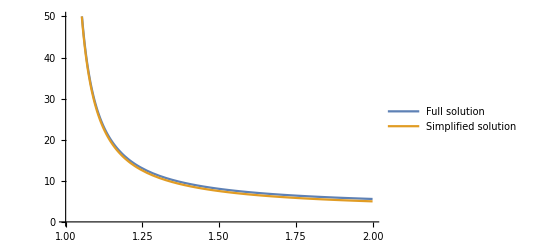

```mathematica
(*Plot complicated and simple solutions for n-star*)
d = 0.8
Plot[{(4 b-d-4 b d+5 b^2 d+√(16 b^2-8 b d+16 b^2 d-8 b^3 d+d^2+8 b d^2-18 b^2 d^2+8 b^3 d^2+b^4 d^2))/(2 (-2 d+2 b d+d^2-2 b d^2+b^2 d^2)), (2 b)/((-1+b) d)}, {b, 1, 2}, PlotLegends->{"Full solution", "Simplified solution"}, PlotRange->{0,50}]
```

```mathematica
Reduce[{n>0&&δ>0&&β*(δ/α*n-1)>δ/α*n}, n]
Reduce[{n>0&&δ>0&&β*(δ/α*n-1)>δ/α*n}, β]
```

δ>0&&((β≤0&&((α<0&&n>0)||(α>0&&0<n<(α β)/(-δ+β δ))))||(0<β<1&&α<0&&n>(α β)/(-δ+β δ))||(β>1&&α>0&&n>(α β)/(-δ+β δ)))

δ>0&&((α<0&&n>0&&β<(n δ)/(-α+n δ))||(α>0&&((0<n<α/δ&&β<(n δ)/(-α+n δ))||(n>α/δ&&β>(n δ)/(-α+n δ)))))

```mathematica
(* Let's calculate β* and n*, assuming different deltas *)
Clear[n1, n2]

(*"simple form" where we do NOT account for chance individuals select each other*)
E11 = (2*b*(n1-1)) / ( b(n1-1)+n2 + (n-n1-n2))
E12 = n2 /  ( b(n1-1)+n2 + (n-n1-n2)) + n2 / (n1+b(n2-1)+(n-n1-n2)) 

Reduce[{n>0&&n1>0&&n2>0&&b>0&&E11>E12}]
```

(2 b (-1+n1))/(n+b (-1+n1)-n1)

n2/(n+b (-1+n1)-n1)+n2/(n+b (-1+n2)-n2)

(0<b<1/2&&((0<n<b&&((0<n2<(2 b^2-2 b n)/(1-3 b+2 b^2)&&0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||(n2≥(2 b^2-2 b n)/(1-3 b+2 b^2)&&n1>0)))||(n==b&&n2>0&&n1>0)||(b<n≤1&&((0<n2<(b-n)/(-1+b)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||((b-n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||(n2≥(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&n1>(b-n)/(-1+b))))||(n>1&&((0<n2<(2 b-2 b n)/(-1+b)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-2 b n)/(-1+b)<n2<(b-n)/(-1+b)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||((b-n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||(n2≥(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&n1>(b-n)/(-1+b))))))||(b==1/2&&((0<n<1/2&&n2>0&&0<n1<(-1/2+n-(3 n2)/2+2 n n2-n2^2/2)/(-1/2+n))||(n==1/2&&n2>0&&n1>0)||(1/2<n≤1&&((0<n2<-2 (1/2-n)&&-2 (1/2-n)<n1<(-1/2+n-(3 n2)/2+2 n n2-n2^2/2)/(-1/2+n))||(-2 (1/2-n)<n2<-2 (3/4-n)+2 √(5/16-n+n^2)&&(0<n1<(-1/2+n-(3 n2)/2+2 n n2-n2^2/2)/(-1/2+n)||n1>-2 (1/2-n)))||(n2≥-2 (3/4-n)+2 √(5/16-n+n^2)&&n1>-2 (1/2-n))))||(n>1&&((0<n2<-2 (1-n)&&(-1/2+n-(3 n2)/2+2 n n2-n2^2/2)/(-1/2+n)<n1<-2 (1/2-n))||(-2 (1-n)<n2<-2 (1/2-n)&&-2 (1/2-n)<n1<(-1/2+n-(3 n2)/2+2 n n2-n2^2/2)/(-1/2+n))||(-2 (1/2-n)<n2<-2 (3/4-n)+2 √(5/16-n+n^2)&&(0<n1<(-1/2+n-(3 n2)/2+2 n n2-n2^2/2)/(-1/2+n)||n1>-2 (1/2-n)))||(n2≥-2 (3/4-n)+2 √(5/16-n+n^2)&&n1>-2 (1/2-n))))))||(1/2<b<1&&((0<n≤b&&n2>0&&0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||(b<n≤1&&((0<n2<(b-n)/(-1+b)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||((b-n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&n1>(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))))||(1<n<b/(-1+2 b)&&((0<n2<(2 b-2 b n)/(-1+b)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-2 b n)/(-1+b)<n2<(b-n)/(-1+b)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||((b-n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&n1>(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))))||(n==b/(-1+2 b)&&((0<n2<(2 b-2 b n)/(-1+b)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-2 b n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&n1>(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))))||(n>b/(-1+2 b)&&((0<n2<(b-n)/(-1+b)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((b-n)/(-1+b)<n2<(2 b-2 b n)/(-1+b)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))||(n2==(2 b-2 b n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))||((2 b-2 b n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&n1>(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))))))||(b==1&&((0<n<1&&n2>0&&0<n1<(-2+2 n-2 n2+2 n n2)/(-2+2 n))||(n>1&&n2>0&&n1>(-2+2 n-2 n2+2 n n2)/(-2+2 n))))||(b>1&&((0<n<1/2&&((0<n2<(b-n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((b-n)/(-1+b)<n2<(2 b^2-2 b n)/(1-3 b+2 b^2)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||((2 b^2-2 b n)/(1-3 b+2 b^2)≤n2≤(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&n1>(b-n)/(-1+b))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)<n2<(2 b-2 b n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||(n2==(2 b-2 b n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))||(n2>(2 b-2 b n)/(-1+b)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))))||(n==1/2&&((0<n2<(-1/2+b)/(-1+b)&&(0<n1<(b-2 b^2+n2-4 b n2+2 b^2 n2-n2^2+b n2^2)/(b-2 b^2+n2-3 b n2+2 b^2 n2)||n1>(-1/2+b)/(-1+b)))||((-1/2+b)/(-1+b)<n2<(-b+2 b^2)/(1-3 b+2 b^2)&&(-1/2+b)/(-1+b)<n1<(b-2 b^2+n2-4 b n2+2 b^2 n2-n2^2+b n2^2)/(b-2 b^2+n2-3 b n2+2 b^2 n2))||(n2>(-b+2 b^2)/(1-3 b+2 b^2)&&(0<n1<(-1/2+b)/(-1+b)||n1>(b-2 b^2+n2-4 b n2+2 b^2 n2-n2^2+b n2^2)/(b-2 b^2+n2-3 b n2+2 b^2 n2)))))||(1/2<n<b/(-1+2 b)&&((0<n2<(b-n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((b-n)/(-1+b)<n2<(2 b-2 b n)/(-1+b)&&(b-n)/(-1+b)<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))||((2 b-2 b n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&0<n1<(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))))||(n==b/(-1+2 b)&&((0<n2<(2 b-2 b n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||((2 b-2 b n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&0<n1<(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))))||(b/(-1+2 b)<n<1&&((0<n2<(2 b-2 b n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(b-n)/(-1+b)))||(n2==(2 b-2 b n)/(-1+b)&&(0<n1<(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))||((2 b-2 b n)/(-1+b)<n2<(b-n)/(-1+b)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))||((b-n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&0<n1<(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))))||(1≤n<b&&((0<n2<(b-n)/(-1+b)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))||((b-n)/(-1+b)<n2<(2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)&&(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)<n1<(b-n)/(-1+b))||((2 b-b^2-n)/(-1+b)+√((2 b^2-2 b^3+b^4-2 b n+n^2)/(-1+b)^2)≤n2≤(2 b^2-2 b n)/(1-3 b+2 b^2)&&0<n1<(b-n)/(-1+b))||(n2>(2 b^2-2 b n)/(1-3 b+2 b^2)&&(0<n1<(b-n)/(-1+b)||n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2)))))||(n≥b&&n2>0&&n1>(-2 b^2+2 b n-4 b n2+2 b^2 n2+2 n n2-n2^2+b n2^2)/(-2 b^2+2 b n+n2-3 b n2+2 b^2 n2))))

```mathematica
β(Subscript[δ,1]/α*n-1) > Subscript[δ,2]/α*n

Reduce[{n>0&&Subscript[δ,1]>0&&Subscript[δ,2]>0&&α>0&&β(Subscript[δ,1]/α*n-1) > Subscript[δ,2]/α*n}, β]
Reduce[{β>0&&Subscript[δ,1]>0&&Subscript[δ,2]>0&&α>0&&β(Subscript[δ,1]/α*n-1) > Subscript[δ,2]/α*n}, n]
```

β (-1+(n δ_1)/α)>(n δ_2)/α

δ_1>0&&α>0&&((0<n<α/δ_1&&δ_2>0&&β<(n δ_2)/(-α+n δ_1))||(n>α/δ_1&&δ_2>0&&β>(n δ_2)/(-α+n δ_1)))

δ_1>0&&δ_2>0&&((0<β<δ_2/δ_1&&α>0&&n<(α β)/(β δ_1-δ_2))||(β>δ_2/δ_1&&α>0&&n>(α β)/(β δ_1-δ_2)))